```mathematica
Clear[x]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

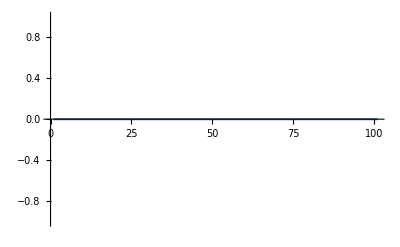

```mathematica
nPoints=101;
data = N@Table[0,{x,0,Pi,Pi/(nPoints-1)}]
ListLinePlot[data]
```

```mathematica
(*subpowers*)
folderDriveName="C:\\Users\\apc\\Documents\\Python Scripts\\Cold Control Heavy\\waveforms\\new_Tom\\Tophat\\"<>ToString[nPoints]<>" long"
If[DirectoryQ[folderDriveName],None,CreateDirectory[folderDriveName]]
δ=10^-5;
Table[
Export[folderDriveName<>"\\tophat_"<>ToString[i]<>"_"<>ToString@Length@data<>".csv",N@Chop[{i/100 data},δ]],
{i,5,100,5}
]
```

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long

C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long

{C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_5_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_10_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_15_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_20_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_25_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_30_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_35_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_40_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_45_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_50_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_55_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_60_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_65_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_70_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_75_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_80_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_85_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_90_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_95_101.csv,C:\Users\apc\Documents\Python Scripts\Cold Control Heavy\waveforms\new_Tom\Tophat\101 long\tophat_100_101.csv}